
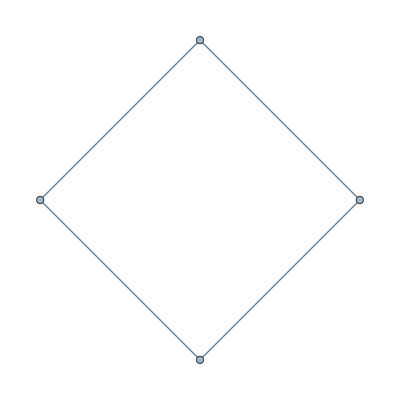
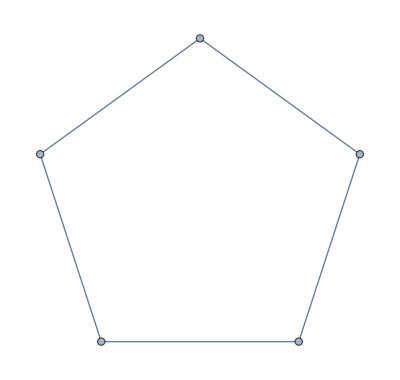
{-Graphics-→{-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[With[{g=CycleGraph[k]},Framed[g, FrameStyle->{Red,Thick}]-> Map[SymbolToGraph,FindFullFormula[g]]],{k,3,6^□}]
```

```mathematica
Table[With[{g=CycleGraph[k]},k-> Length[FindFullFormula[g]]],{k,3,9}]
```

{3→1,4→4,5→11,6→41,7→162,8→715,9→3425}